```mathematica
pCOM=1/2 √(mX^2-4 me^2);
pCOM^2=1/4(mX^2-4 me^2);
β=(√(EX^2-mX^2))/EX;
β^2=(EX^2-mX^2)/EX^2;
γ=EX/mX;
p4eplusCOM=(1/2 mX,pCOM sin θ,pCOM cos θ);
p4eminusCOM=(1/2 mX,-pCOM sin θ,-pCOM cos θ);
p4eplus=(γ(1/2 mX+β pCOM cos θ),pCOM sin θ,γ (pCOM cos θ+ β 1/2 mX));
p4eminus=(γ(1/2 mX-β pCOM cos θ),-pCOM sin θ,-γ (pCOM cos θ- β 1/2 mX));
cθeplus=(γ (pCOM cos θ+ β 1/2 mX))/(√(pCOM^2 sin θ^2+γ^2(pCOM cos θ+ β 1/2 mX)^2));
sθeplus=(pCOM sin θ)/(√(pCOM^2 sin θ^2+γ^2(pCOM cos θ+ β 1/2 mX)^2));

cθeminus=(-γ (pCOM cos θ- β 1/2 mX))/(√(pCOM^2 sin θ^2+γ^2(pCOM cos θ- β 1/2 mX)^2));
sθeminus=(pCOM sin θ)/(√(pCOM^2 sin θ^2+γ^2(pCOM cos θ- β 1/2 mX)^2));
cθee=(((EX^2-mX^2)(1/4 mX^2-1/4(mX^2-4 me^2)cosθ^2))/mX^2 -1/4(mX^2-4 me^2) )/(√(1/4(mX^2-4 me^2)(1-cosθ^2)+(EX/mX)^2(1/2 √(mX^2-4 me^2) cosθ+ (√(EX^2-mX^2))/EX 1/2 mX)^2)√(1/4(mX^2-4 me^2)(1-cosθ^2)+(EX/mX)^2(1/2 √(mX^2-4 me^2) cosθ- (√(EX^2-mX^2))/EX 1/2 mX)^2))
cθee=(-(EX/mX)^2(1/4(mX^2-4 me^2)cosθ^2- (EX^2-mX^2)/EX^2 1/4 mX^2)-1/4(mX^2-4 me^2) (1-cosθ^2))/(√(-me^2+((cosθ √(EX^2-mX^2)√(mX^2-4 me^2))/(2mX)+EX/2)^2)√(-me^2+((cosθ √(EX^2-mX^2)√(mX^2-4 me^2))/(2mX)-EX/2)^2))
```

```mathematica
Series[(-(EX/mX)^2(1/4(mX^2-4 me^2)cosθ^2- (EX^2-mX^2)/EX^2 1/4 mX^2)-1/4(mX^2-4 me^2) (1-cosθ^2))/(√(-me^2+((cosθ √(EX^2-mX^2)√(mX^2-4 me^2))/(2mX)+EX/2)^2)√(-me^2+((cosθ √(EX^2-mX^2)√(mX^2-4 me^2))/(2mX)-EX/2)^2)),{cosθ,0,1}]
```

(EX^2+4 me^2-2 mX^2)/(EX^2-4 me^2)+O[cosθ]^2

```mathematica
angle[mX_,γ_,cosθ_]:=ArcCos[(-γ^2(1/4(mX^2-4 me^2)cosθ^2- (1-1/γ^2) 1/4 mX^2)-1/4(mX^2-4 me^2) (1-cosθ^2))/(√(-me^2+((cosθ √(mX^2 γ^2-mX^2)√(mX^2-4 me^2))/(2mX)+(mX γ)/2)^2)√(-me^2+((cosθ √(mX^2 γ^2-mX^2)√(mX^2-4 me^2))/(2mX)-(mX γ)/2)^2))/.{me->5.11*10^-4}];
```

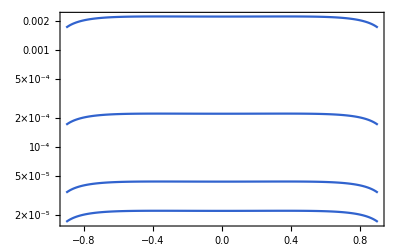
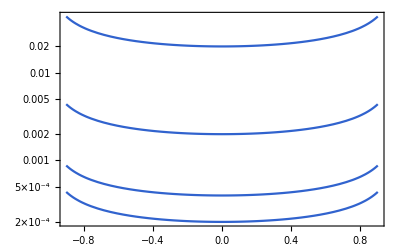
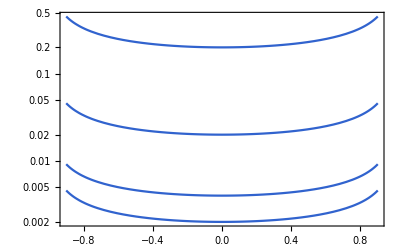

```mathematica
Table[

LogPlot[
Table[
angle[mx,engk,c],
{engk,{1,10,50,100}}],
{c,-0.9,0.9},ImageSize->400,PlotRange->All,Axes->True]
,{mx,{0.0015,0.01,0.1}}]
```

```mathematica
angle[0.3,10,0]
```

0.0600087

```mathematica
2*0.3/10
```

0.06

```mathematica
Clear[β,γ]
me=0.000511;
pCOM[mX_]:=1/2 √(mX^2-4 me^2);
β[γ_]:=√(1-1/γ^2);
```

```mathematica
cθeplus[cosθ_,γ_,mX_]:=(γ (pCOM[mX] cosθ+ β[γ] 1/2 mX))/(√(pCOM[mX]^2 (1-cosθ^2)+γ^2(pCOM[mX] cosθ+ β[γ] 1/2 mX)^2));
```

```mathematica
cθeplus[Cos[0.01],10]
```

1.

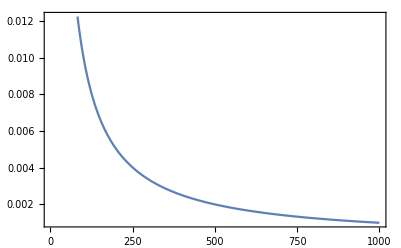

```mathematica
Plot[ArcCos[cθeplus[0,x]],{x,1,1000}]
```

```mathematica
ArcCos[cθeplus[0.5,10/0.02]]
```

0.00115446

```mathematica
ArcCos[(γ (pCOM cosθ+ β 1/2 mX))/(√(pCOM^2 sinθ^2+γ^2(pCOM cosθ+ β 1/2 mX)^2))/.{γ->10/0.02,pCOM->(√(0.02^2-4*0.000511^2))/2,β->√(1-0.02/10),cosθ->0.5,sinθ->√(1-0.5^2),mX->0.02}]
```

0.00115446

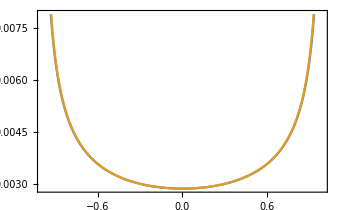

```mathematica
Plot[{angle[0.02,700,c],angle[0.2,700,c]},{c,-0.99,0.99}]
```

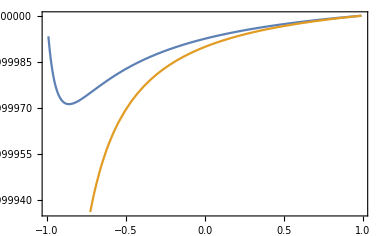

```mathematica
Plot[{cθeplus[c,700,0.002],cθeplus[c,700,0.2]},{c,-0.99,0.99}]
```